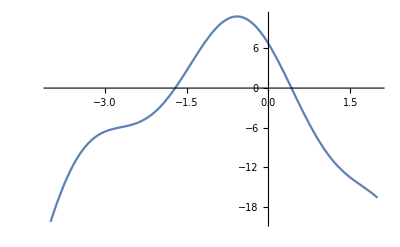

```mathematica
f[x_]:=5Cos[2x+1]-3 x^2-5x+4;
Plot[f[x],{x,-4,2}]
```

```mathematica
x0=0.5;
x1=x0-f[x0]/f'[x0];
i = 1;
eps=0.001;

While[Abs[x1-x0]>eps,
x0=x1;
x1=x0-f[x0]/f'[x0];
i++];
Round[x1, eps]
i
```

0.422

2

```mathematica
ClearAll;
x0=0.5;
x1=2;
x2=x1-(f[x1]*(x1-x0))/(f[x1]-f[x0]);
i = 1;
eps=0.001;

While[Abs[x1-x0]>eps,
x0=x1;
     x1=x2;
     x2=x1-(f[x1]*(x1-x0))/(f[x1]-f[x0]);
i++];
Round[x2, eps]
i
```

0.422

5